```mathematica
Archimedes's method of estimating π
```

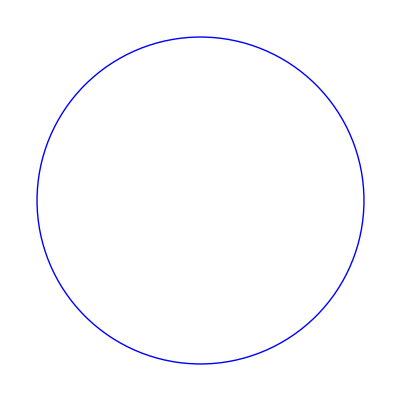

```mathematica
(* A circle of radius 1/2 *)
r=1/2;
Graphics[{Blue,Circle[{0,0},r]}]
```

```mathematica
(* Its inscribed triangle: *)
n=3;
angles=Table[k/n 2π,{k,0,n-1}]
```

{0,(2 π)/3,(4 π)/3}

```mathematica
points={r Cos[#], r Sin[#]}&/@angles
```

{{1/2,0},{-1/4,(√3)/4},{-1/4,-(√3)/4}}

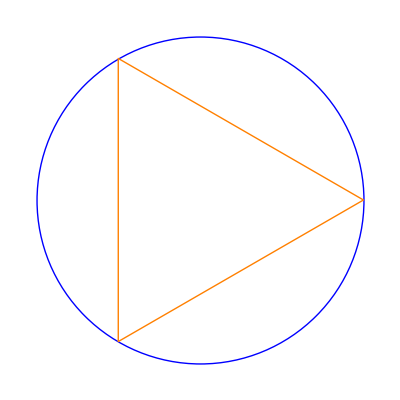

```mathematica
Graphics[{{Blue,Circle[{0,0},r]},{Orange,Line[Append[points, points⟦1⟧]]}}]
```

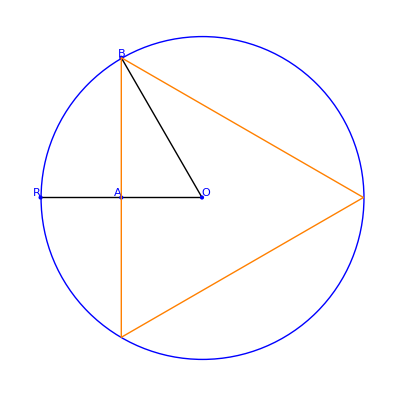

```mathematica
(* Archimedes method for the inscribed polygon: *)
Graphics[{Line[{{-r,0}, {0,0},{-r/2,√3/2r}}],{Blue,{Text["R",{-r-r/40,r/40}],Point[{-r,0}],Text["A",{-r/2-r/40,r/40}],Point[{-r/2,0}],Text["B",{-r/2,√3/2r+r/40}],Point[{-r/2,√3/2r}],Text["O",{r/40,r/40}],Point[{0,0}],Circle[{0,0},r]}}, Table[{Orange,{as=Table[k/n 2π,{k,0,n-1}];ps={r Cos[#], r Sin[#]}&/@as;Line[Append[ps, ps⟦1⟧]]}}, {n,3,3}]}]
```

```mathematica
(* For and inscribed triangle: *)
AO=R/2
```

R/2

```mathematica
AB=√(R^2-AO^2)
```

1/2 √3 √(R^2)

```mathematica
AB/.R-> 1
```

(√3)/2

```mathematica
(* So, the side length of the inscribed triangle is: *)
2AB/.R-> 1
```

√3

```mathematica
(*
  If you know the half-side AB of an inscribed polygon of N sides, you can easily compute the side length (BR) of the inscribed polygon of 2N sides.
So, starting with the triangle, and doubling each time, you don't need more than Pythagoras's theorem to compute these polygon perimeters.

The same with the circumscribed polygon, below.
*)
```

```mathematica
(* So: *)
Manipulate[Column[{Row[{"Sides:",n}],Graphics[{{Blue,Circle[{0,0},r]},{Orange,{as=Table[k/n 2π,{k,0,n-1}];ps={r Cos[#], r Sin[#]}&/@as;Line[Append[ps, ps⟦1⟧]]}}}, ImageSize->Medium], chord=2r Sin[θ/2]/.θ-> as⟦2⟧; Row[{"Perimeter: ",n chord}]}],{n, 3, 96, AnimationRate->2/3}, {r, 1/2}]
```

```mathematica
(* Circumscribed polygon *)
(* Equation of the circle: *)
r=.
Solve[x^2+y^2==r^2,y]
```

{{y→-√(r^2-x^2)},{y→√(r^2-x^2)}}

```mathematica
circle[x_]:= √(r^2-x^2)
```

```mathematica
(* radial line: *)
ϵ=10^-6;
rl[x_, θ_]:=Tan[θ] x
```

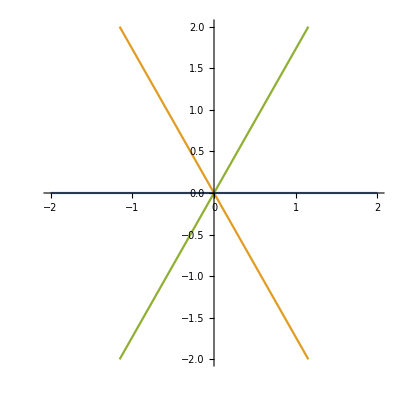

```mathematica
r=1/2;
Plot[rl[x,θ+ϵ]/.θ-> angles, {x, -4r, 4r},{PlotRange-> {{-2,2}, {-2,2}}, AspectRatio-> 1,Evaluated->True}]
```

```mathematica
(* Use the perpendicular line at the radius boundary (which is the tangent): *)
r=.
θ=.
pl[x_, θ_]:= Tan[θ+π/2](x-r Cos[θ])+r Sin[θ]
pl[x, θ]
```

-((x-r Cos[θ]) Cot[θ])+r Sin[θ]

```mathematica
TrigReduce[-(x-r Cos[θ]) Cot[θ]+r Sin[θ]]
```

1/2 (2 r-2 x Cot[θ] Csc[θ]+r Csc[θ]^2+r Cos[2 θ] Csc[θ]^2) Sin[θ]

```mathematica
Simplify[1/2 (2 r-2 x Cot[θ] Csc[θ]+r Csc[θ]^2+r Cos[2 θ] Csc[θ]^2) Sin[θ]]
```

(r-x Cos[θ]) Csc[θ]

```mathematica
pl[x_, θ_]:= (r-x Cos[θ]) Csc[θ]
```

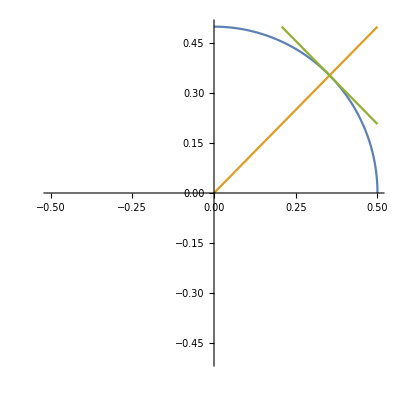

```mathematica
r=1/2;
Plot[{circle[x], rl[x,θ], pl[x,θ]}/.θ-> π/4, {x, 0,r}, {AspectRatio->1, Evaluated->True, PlotRange->{{-r,r}, {-r,r}}}]
```

```mathematica
(* Now, solve the equality between the radial line at the angle, and the perpendicular line at the half angle (or the other way around) *)
r=.;
Solve[rl[x, θ]==pl[x, hθ], x]//Flatten//FullSimplify
```

{x→r Cos[θ] Sec[hθ-θ]}

```mathematica
(* So:*)
n=3;
r=1/2;
```

```mathematica
as=Table[k/n 2π,{k,0,n-1,1}]
```

{0,(2 π)/3,(4 π)/3}

```mathematica
has=Table[k/(2n)2π,{k,1,2n-1,2}]
```

{π/3,π,(5 π)/3}

```mathematica
rl[x, θ]
```

x Tan[θ]

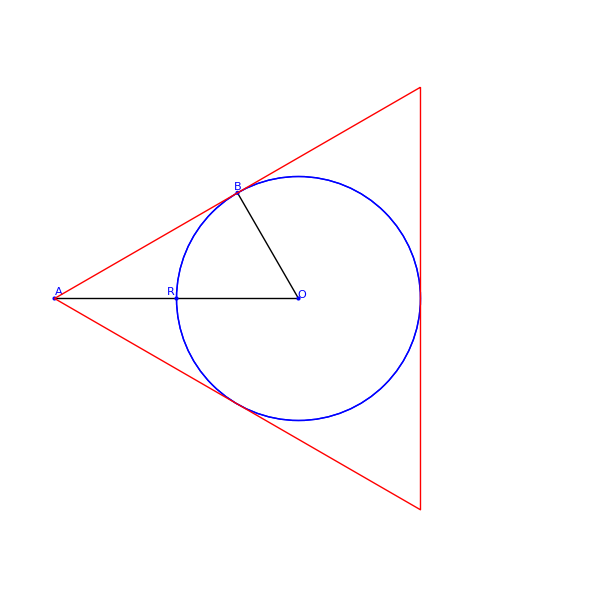

```mathematica
(* Archimedes method for the circumscribed polygon: *)
Graphics[{Line[{{-2r,0}, {0,0},{-r/2,√3/2r}}],{Blue,{Text["R",{-r-r/20,r/20}],Point[{-r,0}],Text["A",{-2r+r/30,r/20}],Point[{-2r,0}],Text["B",{-r/2,√3/2r+r/20}],Point[{-r/2,√3/2r}],Text["O",{r/40,r/40}],Point[{0,0}],Circle[{0,0},r]}},{Blue,Circle[{0,0},r]},{Red,as=Table[k/n 2π,{k,0,n-1,1}];
ps={r Cos[#], r Sin[#]}&/@as;
has=Table[k/(2n)2π,{k,1,2n-1,2}];
pxs=r Cos[#⟦1⟧+ϵ] Sec[#⟦2⟧-#⟦1⟧+ϵ]&/@MapThread[{#1,#2}&, {has,as}];
pys=#⟦1⟧Tan[#⟦2⟧+ϵ]&/@MapThread[{#1,#2}&, {pxs,has}];
sps=MapThread[{#1, #2}&,{pxs, pys}];
Line[Append[sps, sps⟦1⟧]]
}},{AspectRatio->1, PlotRange->{{-2r,2r},{-2r,2r}}}]
```

```mathematica
(* For the circumscribed triangle: *)
AO=2R
```

2 R

```mathematica
AB=√(AO^2-R^2)
```

√3 √(R^2)

```mathematica
AB/.R-> 1
```

√3

```mathematica
(* So, the side length of the circumscribed triangle is: *)
2 AB/.R-> 1
```

2 √3

```mathematica
(* And manipulate it: *)
Manipulate[Column[{Row[{"Sides:",n}],Graphics[{{Blue,Circle[{0,0},r]},{Orange,{as=Table[k/n 2π,{k,0,n-1,1}];
ps={r Cos[#], r Sin[#]}&/@as;
Line[Append[ps, ps⟦1⟧]]}},
{Red,{has=Table[k/(2n)2π,{k,1,2n-1,2}];
pxs=r Cos[#⟦1⟧+ϵ] Sec[#⟦2⟧-#⟦1⟧+ϵ]&/@MapThread[{#1,#2}&, {has,as}];
pys=#⟦1⟧Tan[#⟦2⟧+ϵ]&/@MapThread[{#1,#2}&, {pxs,has}];
sps=MapThread[{#1, #2}&,{pxs, pys}];
Line[Append[sps, sps⟦1⟧]]
}}},{AspectRatio->1, PlotRange->{{-2r,2r},{-2r,2r}}, ImageSize->Medium}],ichord=2r Sin[θ/2]/.θ-> as⟦2⟧; Row[{"Inner Perimeter: ",n ichord}], ochord=2r Tan[θ/2]/.θ-> as⟦2⟧; Row[{"Outer Perimeter: ",n ochord}],Row[{"Mean Perimeter: ",n (ichord+ochord)/2}]}],{n, 3, 96, AnimationRate->2/3}, {r, 1/2}]
```

```mathematica
π//N
```

3.14159

```mathematica
22/7//N
```

3.14286